```mathematica
ClearAll["Global`*"];
Dg0 = 7.6 * 10^-10;(*25C Glutamate diffusion constant [m^2/s](Rusakov 2011)*)
kb=1.380649*10^-23; (*Boltzmann constant [m^2 kg s^-2 K^-1]*)
T25 =298.20;(*25C in Kelvin*)
T30=303.15; (*30C in Kelvin*)
η=0.001; (*Pa s*)
n=3; (*Number of (relevant) dimensions for diffusion*)
Df[r_,T_]:=(kb*T)/(6*π*η*r); (*Diffusion constant from stokes einstein relation*)
td= 45*60; (*Doubling time in seconds*)
N0[x] =1/(7*10^-6) *x;(* Cell density [m^-1], one cell per 7 μm*)
Vcell = 10^-18 ;(*Single cell volume [m^3], 1fL*)
cgc =150;(*Basal cell glutamate concentration [mol m^-3]*)
cgm =34;(*Basal media glutamate concentration 34mM [mol m^-3]*)
ks =cgm*0.5;(*Minimum glutamate concentration that can sustain cell max uptake rate[mol m^-3], same as half velocity constant*)
αmax =cgc/td; (*per capita uptake rate, [mol m^-3 s^-1 ]*)
De=1/4*Dg0; (*Effective diffusion in a biofilm*)
nh [c90_,c10_]:=FullSimplify[Log[10,81]/Log[10,c90/c10] ]; (*Hill equation coefficient, where c90 and c10 must be emperically measured as the concentrations where 90 and 10 percent of max uptake occurs*)
Lmax=1000*10^-6; (*Max distance for opposite wall of chamber*)
nmod=nh[.9,.1];
(*Steady state solution, assuming concentration dependent uptake according to order nmod hill equation*)
simplesoln [c0_,l_]:= DSolve[{De*∇_{x}^2 c[x]-αmax*c[x]/cgm==0, c[0]==c0,c'[l]==0},c[x],{x,0,l}]
numsoln[c0_,l_]:=NDSolve[{De*∇_{x}^2 c[x]-αmax*(c[x])^nmod/(ks^nmod+(c[x])^nmod)==0, c[0]==c0,c'[l]==0},c[x],x];
(*`````````````````````````````````````````````````````````````````````````````````````````````````*)
```

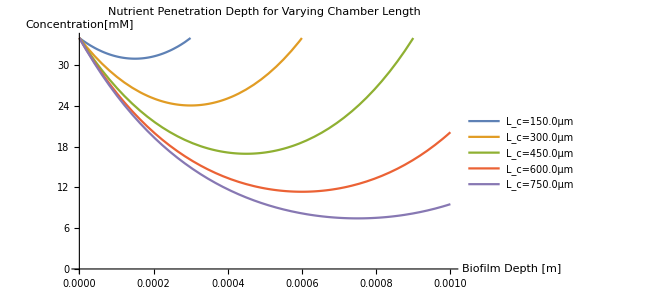

```mathematica
(*Steady state solution, assuming some basic concentration dependent uptake*)
nL=5;
L0=0.75*Lmax/nL;
Legendlist={};
Do[AppendTo[Legendlist,"L_c="<>TextString[i*L0*10^6]<>"μm"],{i,1,nL}]
tabexpr=Table[c[x]/.simplesoln[cgm,i*L0][[1]],{i,1,nL}];
Plot [tabexpr,{x,0,Lmax},AxesLabel->{"Biofilm Depth [m]","Concentration[mM]"},PlotRange->{{0,Lmax},{0,cgm}},PlotLabel->"Nutrient Penetration Depth for Varying Chamber Length",PlotLegends->Legendlist]
```

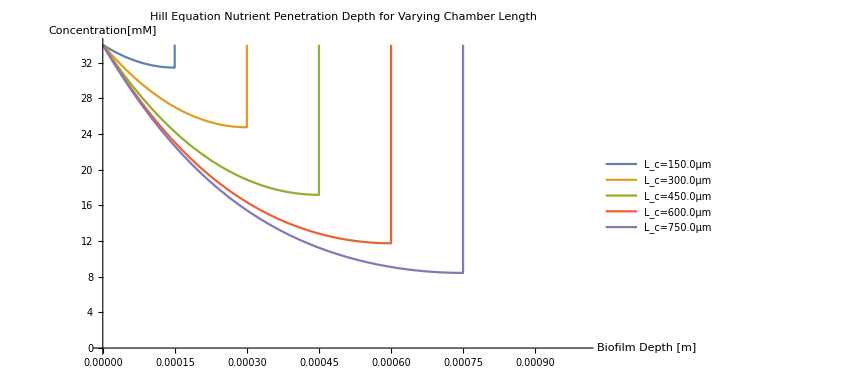

```mathematica
(*`````````````````````````````````````````````````````````````````````````````````````````````````*) 
(*Steady state solution, assuming concentration dependent uptake according to order nmod Hill equation*)
nL=5;
L0=0.75Lmax/nL;
Legendlist={};
Do[AppendTo[Legendlist,"L_c="<>TextString[i*L0*10^6]<>"μm"],{i,1,nL}]
tabexpr=Table[c[x]/.numsoln[cgm,i*L0][[1]],{i,1,nL}];
Plot [tabexpr,{x,0,Lmax},AxesLabel->{"Biofilm Depth [m]","Concentration[mM]"},PlotRange->{{0,Lmax},{0,cgm}},PlotLabel->"Hill Equation Nutrient Penetration Depth for Varying Chamber Length",PlotLegends->Legendlist]
```

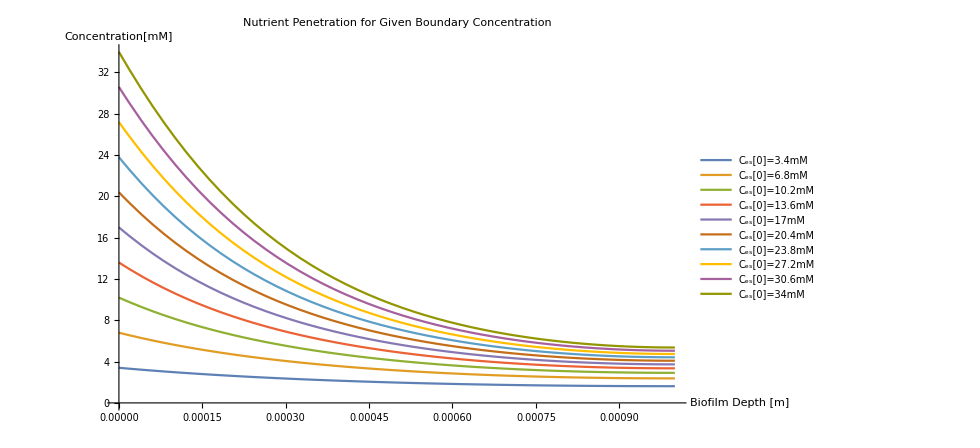

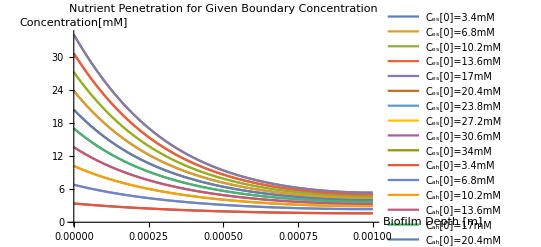

```mathematica
(*`````````````````````````````````````````````````````````````````````````````````````````````````*) 
(*Steady state solution, assuming concentration dependent uptake according to order nmod Hill equation*)
(*Exact simple*)
nL=10;
c0=cgm/nL;
Legendlist={};
exprlist={};
Do[AppendTo[Legendlist,"C_es[0]="<>TextString[i*c0]<>"mM"],{i,1,nL}]
Do[AppendTo[exprlist,c[x]/.numsoln[i*c0,Lmax][[1]]],{i,1,nL}]
Plot [exprlist,{x,0,Lmax},AxesLabel->{"Biofilm Depth [m]","Concentration[mM]"},PlotRange->{{0,Lmax},{0,cgm}},PlotLabel->"Nutrient Penetration for Given Boundary Concentration",PlotLegends->Legendlist]

(*Approximate Hill*)
Do[AppendTo[Legendlist,"C_ah[0]="<>TextString[i*c0]<>"mM"],{i,1,nL}]
Do[AppendTo[exprlist,c[x]/.numsoln[i*c0,Lmax][[1]]],{i,1,nL}]
Plot [exprlist,{x,0,Lmax},AxesLabel->{"Biofilm Depth [m]","Concentration[mM]"},PlotRange->{{0,Lmax},{0,cgm}},PlotLabel->"Nutrient Penetration for Given Boundary Concentration",PlotLegends->Legendlist]
```